```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot},GridLines->Automatic];
```

# Finite Fields

https://en.wikipedia.org/wiki/Finite_field

https://youtu.be/X63MWZIN3gM
-Graphics-
https://youtu.be/nm_o0IS2gK4
-Graphics-
https://youtu.be/Rir4DM3Y9hE
-Graphics-
https://www.youtube.com/live/hkHW_mbLJtc?feature=share
-Graphics-

### Number fields

#### Infinite fields

ℚ = {0,1,11,-11, -2/7, ... };
ℝ = {0,1,11,-11,-2/7,√2,(1+√2)^(1/3),π, ⅇ,1.01001000100001..,...}
ℂ = {0, 1,... π,..., 1.5 - 4.1 ⅈ,  √1.2 - 3 ⅈ,...};
ℝ[x]={P[x]/Q[x]| P,Q are polinomials , coeffs in ℝ,Q≠0};
ℚ[x], ℂ[x];

ℚ ⊂ℝ⊂ℂ;
ℚ⊂ℚ[x], ℝ⊂ℝ[x], ℂ ⊂ℂ[x];

#### Not fields – division is not defined (not for all)

ℕ = {1, 2, 3, 4, ...}; (* problems with subtraction and division *)
ℤ = {0, -1, 1, 2, -2, 3, -3, ...};  (* problems only with division *)
ℤ (x) = {0,1,-7,113, 3+x,2-5 x^2, x+x^3+x^6, 1000 x^1000,...}
ℤ (x) = {P[x] | P  is polynomial of x, coeffs in ℤ};  (* problems only with division *)
ℤ (x), ℚ (x),  ℝ (x) – rings of polynomials.
ℕ ⊂ ℤ ⊂ ℚ⊂ ℝ ⊂ ℂ 
ℂ could be constructed as equivalence classes in ℝ (x).

#### Finite fields

𝔽_2,𝔽_3,𝔽_4,𝔽_5,𝔽_7,𝔽_8,𝔽_9,𝔽_11,𝔽_13,𝔽_16,𝔽_17,...
𝔽_2⊂𝔽_4⊂𝔽_8⊂𝔽_16 ...;
𝔽_n has n elements.
They are not subsets of any of the fields ℚ,ℝ, ℂ. 
But they could be constructed as equvalence classes in ℤ or ℤ(x);

You have set of  n objects.
How to define × and + so that they behave like numbers?

### 𝔽_p

```mathematica
p=13;
Table[Mod[x + y,p],{x,0,p-1},{y,0,p-1}]//Grid[#,Frame->All]&
```

0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 0
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 0 | 1
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 0 | 1 | 2
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 0 | 1 | 2 | 3
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 0 | 1 | 2 | 3 | 4
6 | 7 | 8 | 9 | 10 | 11 | 12 | 0 | 1 | 2 | 3 | 4 | 5
7 | 8 | 9 | 10 | 11 | 12 | 0 | 1 | 2 | 3 | 4 | 5 | 6
8 | 9 | 10 | 11 | 12 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
9 | 10 | 11 | 12 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
10 | 11 | 12 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
11 | 12 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
12 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11

```mathematica
p=13;
Table[Mod[x * y,p],{x,0,p-1},{y,0,p-1}]//Grid[#,Frame->All]&
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
0 | 2 | 4 | 6 | 8 | 10 | 12 | 1 | 3 | 5 | 7 | 9 | 11
0 | 3 | 6 | 9 | 12 | 2 | 5 | 8 | 11 | 1 | 4 | 7 | 10
0 | 4 | 8 | 12 | 3 | 7 | 11 | 2 | 6 | 10 | 1 | 5 | 9
0 | 5 | 10 | 2 | 7 | 12 | 4 | 9 | 1 | 6 | 11 | 3 | 8
0 | 6 | 12 | 5 | 11 | 4 | 10 | 3 | 9 | 2 | 8 | 1 | 7
0 | 7 | 1 | 8 | 2 | 9 | 3 | 10 | 4 | 11 | 5 | 12 | 6
0 | 8 | 3 | 11 | 6 | 1 | 9 | 4 | 12 | 7 | 2 | 10 | 5
0 | 9 | 5 | 1 | 10 | 6 | 2 | 11 | 7 | 3 | 12 | 8 | 4
0 | 10 | 7 | 4 | 1 | 11 | 8 | 5 | 2 | 12 | 9 | 6 | 3
0 | 11 | 9 | 7 | 5 | 3 | 1 | 12 | 10 | 8 | 6 | 4 | 2
0 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1

```mathematica
a + (b + c) = (a + b) + c;
a+b = b + a;
0 +a = a;
for any a there is  b: a + b ==0;

a * (b * c) = (a * b) * c;
a*b == b*a;
1 *a = a;

(a + b) * c = a * c + b* c;

for any a≠0 there is  b: a * b ==1;
```

Set::write: Tag Plus in a+(b+c) is Protected.

Set::write: Tag Plus in a+b is Protected.

Set::write: Tag Plus in 0+a is Protected.

Set::write: Tag Times in a (b c) is Protected.

Set::write: Tag Times in 1 a is Protected.

Set::write: Tag Times in (a+b) c is Protected.

Lets denote 
b=-a 
a+b=0 
and define subtraction :
a-c means a+ (-c) 

Lets denote 
b=a^-1 
a*b=1 
and define devision :
a/c means a* (c^-1) 

----------
Prove:   -(-a)==a :
	a+(-a)==0 :
Prove:   -a==(-1)*a :
	(-1)*a+a ==(-1)*a+1*a ==(-1 + 1)*a==0 * a == 0,
Prove:   -(a*b)==(-a)*b 
	 -(a*b)==(-1)*(a*b)==((-1) *a)*b =(-a) *b

-----------
Piecewise[{{a≠0,, }, {a*b_1==a*b_2,, }}]
⇒ a*b_1+(-(a b_2))==0,
⇒ a*b_1+(-(a b_2))==0,
⇒ a*(b_1-b_2)==0,
⇒ a^-1 a*(b_1-b_2)==0 
⇒ 1*(b_1-b_2)==0 
⇒ b_1-b_2==0 
⇒ b_1=b_2

#### Rows of multiplication and sum- tables are permutations

if a*b==1
then 
(a*b)*c==c
and then
a*(b*c)==c
a*d==c
so for any a and c, a ≠ 0, and c ≠ 0,  there is d  such that a * d == c.
So each row of multiplication table contains all numbers from {0,1,..., p-1}.

#### There is no divisors of 0: (a *b == 0) => (a == 0 OR b == 0)

a * b == 0;
a^-1*(a * b) == 0;
(a^-1*a) * b == 0;
1 * b == 0
b == 0;

### Solutions for a x + b = 0

x = -b / a;

### Solutions for x^2=a

√a=?

Is there solution for x^2==-1?

```mathematica
primes1k=Prime[Range[1000]];
```

```mathematica
primes10k=Prime[Range[10000]];
```

```mathematica
p=13; 
Mod[Range[1,p-1]^2,p]
```

{1,4,9,3,12,10,10,12,3,9,4,1}

x^2==3 has solutions mod 13
x^2==11 has no solutions mod 13

```mathematica
p=13; 
Mod[Range[1,p-1]^2,p]//DeleteDuplicates
```

{1,4,9,3,12,10}

Only half of numbers  a=1, 2, ..., p-1 has solution x^2==a.

```mathematica
(solData10k=(
p=#;
{p,JacobiSymbol[-1,p]}
)&/@primes10k;)//Timing
{ps,hs}=solData10kᵀ;
```

{0.051409,Null}

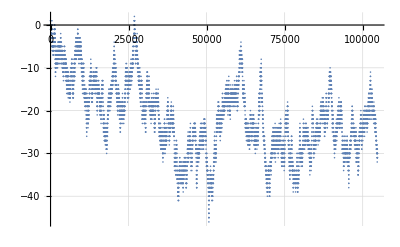

```mathematica
ListPlot[{ps, Accumulate[hs]}ᵀ]
```

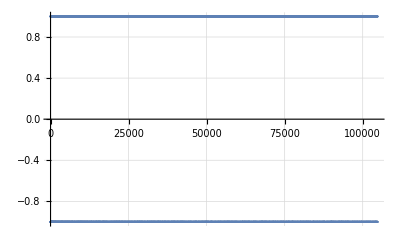

```mathematica
ListPlot[solData10k]
```

```mathematica
Solve[x^2==-1,Modulus->13]
```

{{x→5},{x→8}}

2^2≡ 4 ≡ -1 mod 5

```mathematica
(solData1k=(
p=#;
{p,If[Length[Solve[x^2==-1,Modulus->p]]>0,1,-1]}
)&/@primes1k;)//Timing
{ps,hs}=solData1kᵀ;
```

{0.795215,Null}

```mathematica
HasSqrt[q_,p_]:=HasSqrt[p,q]=If[Length[Solve[x^2==q,Modulus->p]]>1,1,-1];
```

Legendre Symbol == HasSqrt
Mathematica has special function JacobiSymbol – extension of Legendre Symbol.
https://en.wikipedia.org/wiki/Legendre_symbol

HasSqrt[a, p] == JacobiSymbol[a, p]

### Solutions forx^m=a

```mathematica
p=13; 
Mod[Range[1,p-1]^3,p]//DeleteDuplicates
```

{1,8,12,5}

```mathematica
Solve[x^3==8,x,Modulus->17]
```

{{x→2}}

```mathematica
p=17; 
Mod[Range[1,p-1]^3,p]//DeleteDuplicates//Sort
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
p=19; 
Mod[Range[1,p-1]^3,p]//DeleteDuplicates//Sort
```

{1,7,8,11,12,18}

```mathematica
p=23; 
Mod[Range[1,p-1]^3,p]//DeleteDuplicates//Sort
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

Result depends on Mod[p - 1, 3]

```mathematica
p=17;
Table[Mod[x^k,p],{k,0,p-1},{x,1,p-1}]//Grid[#,Frame->All]&
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 4 | 9 | 16 | 8 | 2 | 15 | 13 | 13 | 15 | 2 | 8 | 16 | 9 | 4 | 1
1 | 8 | 10 | 13 | 6 | 12 | 3 | 2 | 15 | 14 | 5 | 11 | 4 | 7 | 9 | 16
1 | 16 | 13 | 1 | 13 | 4 | 4 | 16 | 16 | 4 | 4 | 13 | 1 | 13 | 16 | 1
1 | 15 | 5 | 4 | 14 | 7 | 11 | 9 | 8 | 6 | 10 | 3 | 13 | 12 | 2 | 16
1 | 13 | 15 | 16 | 2 | 8 | 9 | 4 | 4 | 9 | 8 | 2 | 16 | 15 | 13 | 1
1 | 9 | 11 | 13 | 10 | 14 | 12 | 15 | 2 | 5 | 3 | 7 | 4 | 6 | 8 | 16
1 | 1 | 16 | 1 | 16 | 16 | 16 | 1 | 1 | 16 | 16 | 16 | 1 | 16 | 1 | 1
1 | 2 | 14 | 4 | 12 | 11 | 10 | 8 | 9 | 7 | 6 | 5 | 13 | 3 | 15 | 16
1 | 4 | 8 | 16 | 9 | 15 | 2 | 13 | 13 | 2 | 15 | 9 | 16 | 8 | 4 | 1
1 | 8 | 7 | 13 | 11 | 5 | 14 | 2 | 15 | 3 | 12 | 6 | 4 | 10 | 9 | 16
1 | 16 | 4 | 1 | 4 | 13 | 13 | 16 | 16 | 13 | 13 | 4 | 1 | 4 | 16 | 1
1 | 15 | 12 | 4 | 3 | 10 | 6 | 9 | 8 | 11 | 7 | 14 | 13 | 5 | 2 | 16
1 | 13 | 2 | 16 | 15 | 9 | 8 | 4 | 4 | 8 | 9 | 15 | 16 | 2 | 13 | 1
1 | 9 | 6 | 13 | 7 | 3 | 5 | 15 | 2 | 12 | 14 | 10 | 4 | 11 | 8 | 16
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

```mathematica
p=13;
Table[If[x==0,k,Mod[x^k,p]],{k,0,p-1},{x,0,p-1}]//Grid[#,Frame->All]&
```

0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 1 | 4 | 9 | 3 | 12 | 10 | 10 | 12 | 3 | 9 | 4 | 1
3 | 1 | 8 | 1 | 12 | 8 | 8 | 5 | 5 | 1 | 12 | 5 | 12
4 | 1 | 3 | 3 | 9 | 1 | 9 | 9 | 1 | 9 | 3 | 3 | 1
5 | 1 | 6 | 9 | 10 | 5 | 2 | 11 | 8 | 3 | 4 | 7 | 12
6 | 1 | 12 | 1 | 1 | 12 | 12 | 12 | 12 | 1 | 1 | 12 | 1
7 | 1 | 11 | 3 | 4 | 8 | 7 | 6 | 5 | 9 | 10 | 2 | 12
8 | 1 | 9 | 9 | 3 | 1 | 3 | 3 | 1 | 3 | 9 | 9 | 1
9 | 1 | 5 | 1 | 12 | 5 | 5 | 8 | 8 | 1 | 12 | 8 | 12
10 | 1 | 10 | 3 | 9 | 12 | 4 | 4 | 12 | 9 | 3 | 10 | 1
11 | 1 | 7 | 9 | 10 | 8 | 11 | 2 | 5 | 3 | 4 | 6 | 12
12 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

#### Fermat' s small theorem

x^(p-1)==1 has solutions {1,2,3,..., p-1}.
x^p==x has solutions {0,1,2,3,..., p-1}

#### Legendre Symbol

x^((p-1)/2)==1 has solutions {a | ∃ y, y^2==a}.
x^((p-1)/2)==-1 has no solutions {a | ∄ y, y^2==a}.

Legendre Symbol  (m/p)=Piecewise[{{1, if  ∃ y, y^2==m mod p}, {-1, if  ∄ y, y^2==m mod p}}]

(m/p) == m^((p-1)/2)  mod p  (use 1 and -1, not p-1)

(m/p) * (n/p)==((m*n)/p)

(-1/p)=1 OR -1,   == ∃ √a 
p< n
(-1/p)=1         team1 = {5,13,17,29, ... }
(-1/p)=-1      team2 = {3,7,11,19,23, ... }

(# team1(n))/(# team2(n))→ 1, n→ ∞ 
(proved, prime number theorem for arithmetic progressions
Dirichlet and Legendre conjecture and de la Vallée Poussin proved)

# team2(n) > # team1(n) for majority of ns.

Conjecture. 1962, Knapowski and Turan:
As X → ∞, the percentage of integers n <= X for which there are more
primes of team2 up to n than of the team1 goes to 100 %.

#### Image of x^m

if p-1=m*n , then x^m can’t run all numbers {1,2,..,p-1}. 
We have  (x^m)^n=x^(p-1)=1 for all x≠ 0. 
If  x^m  run through all numbers {1,2,..,p-1} then y^n-1 should have p-1 solutions: y=x^m, x = 1,2,3,..., p-1. But polynomial  y^n-1  can’t have more then n different roots.

If GCD[p - 1, m] == 1, than ∃ n: m*n ≡ 1 mod (p-1), and (x^m)^n≡x^(m * n)≡ x^((p-1)k + 1)≡x^1 mod (p).
So x^m  runs through all numbers  {1,2,..,p-1} if GCD[p - 1, m]==1.

#### Home work

1) Find the proof of small Fermat theorem:
					x^(p-1)-1=0  for x ∈ 𝔽_p,x ≠ 0
Notice that numbers {2,3,..., p-2} could be partitioned to pairs of mutually inverse numbers,
and numbers  1 and p-1 are self inverses, so multiplication of all nonzero numbers from 𝔽_p gives -1:
					1*2*3...*(p-1)=-1.	
Consider multiplication of all nonzero numbers from a-th row of multiplication table: 		
				(1*a)*(2*a)*...*((p-1)*a)=-1.
and finish the proof.
2)Proof that  for x ∈ 𝔽_p,x ≠ 0 from (a) (b) and (c)
      (a) x^(p-1)-1=(x^((p-1)/2)-1)(x^((p-1)/2)+1);
      (b) x^(p-1)-1=0   (small Fermat Theorem);
      (c) polynomial with k  different roots has degree ≥   k ;
we can infer Legendre Symbol formula:
	(m/p) == m^((p-1)/2)  mod p  (use 1 and -1, not p-1)

Домашнее задание:
1) Докажите или прочитайте как доказывается малая теорема Ферма:
						x^(p-1)-1=0  for x ∈ 𝔽_p,x ≠ 0
Например, обратите внимание на то, что числа {2,3,..., p-2} разбиваются на пары обратных чисел, а числа  1 и p-1 обратны сами себе, поэтому произведение всех чисел поля кроме 0 равно -1:
					1*2*3...*(p-1)=-1.	
Далее рассмотрите произведение всех чисел из строчки a таблицы умножения: 							(1*a)*(2*a)*...*((p-1)*a)=-1.
и поработайте с этим тождеством.
2) Докажите, что из трёх утверждений для x ∈ 𝔽_p,x ≠ 0
      (a) x^(p-1)-1=(x^((p-1)/2)-1)(x^((p-1)/2)+1);
      (b) x^(p-1)-1=0   (малая теорема Ферма);
      (c) многочлен с  k  разными корнями имеет степень k  или больше;
следует формула для символа Лежандра:
	(m/p) == m^((p-1)/2)  mod p  (use 1 and -1, not p-1)

### Solutions forx^2=a, Prime numbers races!

```mathematica
(* primes10k=Prime[Range[10000]]; *)
```

```mathematica
(* primes3m=Prime[Range[3000000]]; *)
```

```mathematica
(* primes10m=Prime[Range[10000000]]; *)
```

```mathematica
primes = primes10k;
```

```mathematica
(solData=(
p=#;
{p,JacobiSymbol[-1,p]}
)&/@primes;)//Timing
{ps,hs}=solDataᵀ;
```

{0.00695,Null}

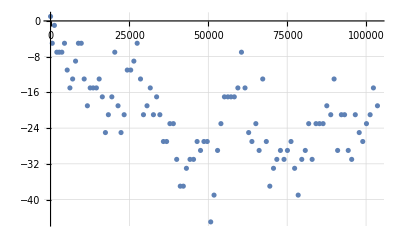

```mathematica
ListPlot[({ps,Accumulate[hs]}ᵀ)[[;;;;100]]]
```

```mathematica
(*
(solData10=(
p=#;
{p,JacobiSymbol[-1,p]}
)&/@primes10m;)//Timing
{ps,hs}=solData10mᵀ;
*)
```

```mathematica
{6.354104,Null};
```

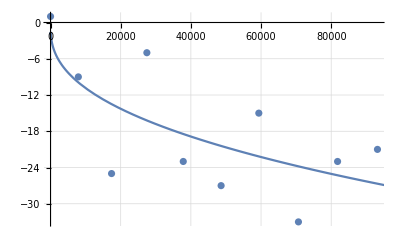

```mathematica
g=ListPlot[({ps,Accumulate[hs]}ᵀ)[[;;;;1000]]];
gB=Plot[-Sqrt[x]/Log[x],{x,2,ps⟦-1⟧}];
Show[g,gB]
```

Chebyshev bias
https://en.wikipedia.org/wiki/Chebyshev%27s_bias
In number theory, Chebyshev’s bias is the phenomenon that most of the time, there are more primes of the form 4k + 3 than of the form 4k + 1, up to the same limit. This phenomenon was first observed by Russian mathematician Pafnuty Chebyshev in 1853.
The stronger conjecture of Knapowski and Turán, that the density of the numbers x for which π(x; 4, 3) > π(x; 4, 1) holds is 1 (that is, it holds for almost all x), turned out to be false. They, however, do have a logarithmic density, which is approximately 0.9959....
PRIME NUMBER RACES, Andrew Granville and Greg Martin
https://arxiv.org/pdf/math/0408319.pdf
Team 1 = primes 4k + 1
Team 3 = primes 4k + 3
Team 1 takes the lead for the first time at prime 26,861. However, since 26,863 is also
prime, Team 3 draws equal and then takes back the lead until
Team 1 gets ahead again at 616,841 and at various numbers until 633,798.
Team 1 gets ahead again at 12,306,137 and at various numbers until 12,382,326.
Team 1 gets ahead again at 951,784,481 and at various numbers until 952,223,506.

```mathematica
(solDataM4=(
p=#;
{p,JacobiSymbol[-4,p]}
)&/@primes;)//Timing
{ps,hs}=solDataM4ᵀ;
```

{0.00709,Null}

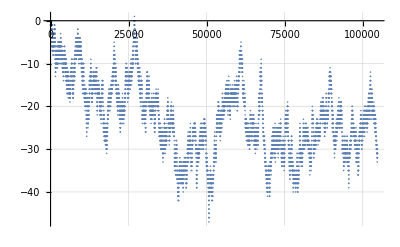

```mathematica
ListPlot[{ps,Accumulate[hs]}ᵀ]
```

```mathematica
(solDataM2=(
p=#;
{p,JacobiSymbol[2,p]}
)&/@primes;)//Timing
{ps,hs}=solDataM2ᵀ;
```

{0.02816,Null}

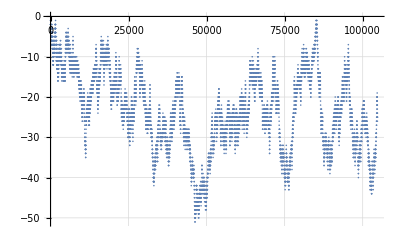

```mathematica
ListPlot[{ps,Accumulate[hs]}ᵀ]
```

### Quadratic reciprocity. Machine Learning to discover the low.

Again about solutions for x^2+a==0

```mathematica
JacobiTable[primes_]:=Module[
{i,j, p,q},
Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
If[JacobiSymbol[p,q]==0,1,JacobiSymbol[p,q]],
{i,Length[primes]},
{j,Length[primes]}
]
]
```

```mathematica
JacobiTable[Prime[Range[10]]]
```

{{1,-1,-1,1,-1,-1,1,-1,1,-1},{-1,1,-1,-1,1,1,-1,-1,1,-1},{-1,-1,1,-1,1,-1,-1,1,-1,1},{1,1,-1,1,-1,-1,-1,1,-1,1},{-1,-1,1,1,1,-1,-1,1,-1,-1},{-1,1,-1,-1,-1,1,1,-1,1,1},{1,-1,-1,-1,-1,1,1,1,-1,-1},{-1,1,1,-1,-1,-1,1,1,-1,-1},{1,-1,-1,1,1,1,-1,1,1,1},{-1,-1,1,1,-1,1,-1,-1,1,1}}

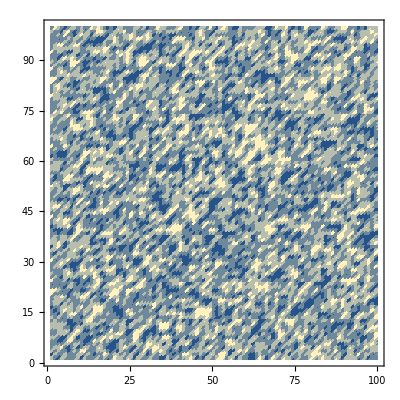

```mathematica
ListDensityPlot[JacobiTable[Prime[Range[100]]]]
```

```mathematica
primes=Prime[Range[3000]];
data=(
p=RandomChoice[primes];
q=RandomChoice[primes];
{p,q, JacobiSymbol[p,q]}
)&/@Range[10000];
```

```mathematica
{fs, target} =((
{p,q,t}=#;
{{
 Mod[p,3],Mod[p,5],Mod[q,3],Mod[q,5],
Mod[(p-1)/2,2], Mod[(q-1)/2,2],
Mod[(p-1)/2,3], Mod[(q-1)/2,3]
}, t}
)&/@ data)ᵀ;
```

```mathematica
StandardDeviation[N[target]]
```

0.999897

```mathematica
model=Predict[fs->target];
Information[model]
```

Predictor information
Data type | Mixed (number: 8)
Standard deviation | 1. ± 0.0013
Method | LinearRegression
Single evaluation time | 2.05 ms/example
Batch evaluation speed | 169. examples/ms
Loss | 1.42 ± 0.001
Model memory | 385. kB
Training examples used | 10000 examples
Training time | 4.88 s
 |

```mathematica
JacobiSimTable[primes_]:=Module[
{i,j, p,q},
Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
JacobiSymbol[p,q]*JacobiSymbol[q,p],
{i,Length[primes]},
{j,Length[primes]}
]
]
```

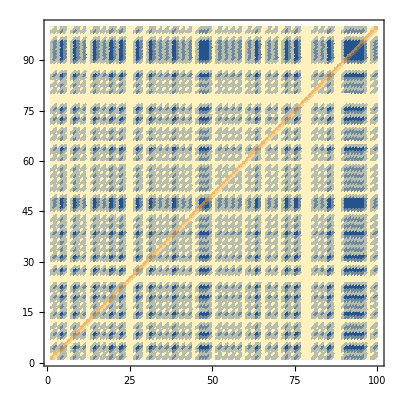

```mathematica
ListDensityPlot[JacobiSimTable[Prime[Range[100]]]]
```

```mathematica
ListDensityPlot[JacobiSimTable[Prime[Range[200]]]]
```

-Graphics-

```mathematica
JacobiSimTable[primes_]:=Module[
{i,j, p,q},
Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
If[JacobiSymbol[p,q]*JacobiSymbol[q,p]==0,1,JacobiSymbol[p,q]*JacobiSymbol[q,p]],
{i,Length[primes]},
{j,Length[primes]}
]
]
```

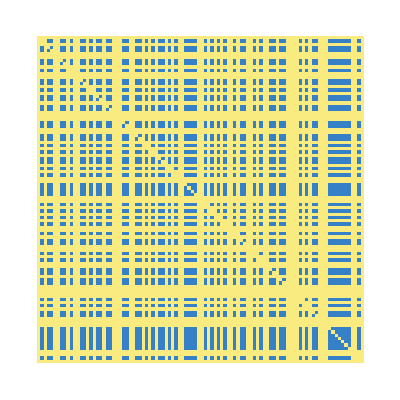

```mathematica
ArrayPlot[1+(1-JacobiSimTable[Prime[Range[100]]])/2,Mesh->False,ColorFunction->Function[{x},{RGBColor[0.98,0.92,0.5], RGBColor[0.21,0.5,0.78] }⟦x+1⟧
]
]
```

```mathematica
primes=Prime[Range[3000]];
data=(
p=RandomChoice[primes];
q=RandomChoice[primes];
{p,q, JacobiSymbol[p,q]*JacobiSymbol[q,p]}
)&/@Range[100000];
```

```mathematica
fullData=((
{p,q,t}=#;
{{
Mod[(p-1)/2,2], Mod[(q-1)/2,2],
Mod[(p-1)/2,3], Mod[(q-1)/2,3],
 Mod[p,3],Mod[p,5],Mod[q,3],Mod[q,5]
}, t}
)&/@ data)//N;
{fs, target} =fullDataᵀ;
{fsT, targetT} =fullData⟦;;80000⟧ᵀ;
{fsV, targetV} =fullData⟦80001;;⟧ᵀ;
```

```mathematica
StandardDeviation[target]
```

0.867307

```mathematica
model=Predict[fs->target];
Information[model]
```

Predictor information
Data type | NumericalVector (length: 8)
Standard deviation | 0.0344 ± 0.0066
Method | DecisionTree
Single evaluation time | 1.11 ms/example
Batch evaluation speed | 662. examples/ms
Loss | -2.9 ± 0.0034
Model memory | 410. kB
Training examples used | 100000 examples
Training time | 5.56 s
 |

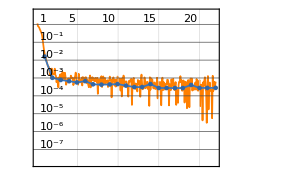
NetTrain Results
summary | ,,  batches:27500  rounds:22  time:15s  examples/s:122707
data | ,,  training examples:80000  validation examples:20000  processed examples:1760000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:4.27×10^-4
validation | ,,  loss:2.8×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netModel = NetTrain[
NetChain[{5,Ramp,4,Ramp,4,Ramp,1}], 
fsT->targetT, All,
ValidationSet-> (fsV->targetV), 
LossFunction->MeanSquaredLossLayer[]
]
```

```mathematica
netModel["TrainingNet"]
```

NetGraph[<>]

```mathematica
fullData=((
{p,q,t}=#;
{{
Mod[(p-1)/2,2], Mod[(q-1)/2,2]
}, t}
)&/@ data)//N;
{fs, target} =fullDataᵀ;
```

```mathematica
model=Predict[fs->target];
Information[model]
```

Predictor information
Data type | NumericalVector (length: 2)
Standard deviation | 0.0536 ± 0.0071
Method | DecisionTree
Single evaluation time | 1.01 ms/example
Batch evaluation speed | 571. examples/ms
Loss | -2.89 ± 0.0037
Model memory | 538. kB
Training examples used | 100000 examples
Training time | 10.6 s
 |

```mathematica
JacobiSim2Table[primes_]:=Module[
{i,j, p,q},
Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
JacobiSymbol[p,q]*JacobiSymbol[q,p] (-1)^((p-1)/2(q-1)/2),
{i,Length[primes]},
{j,Length[primes]}
]
]
```

Carl Friedrich Gauss proved this in 8 different ways, published in 1801.

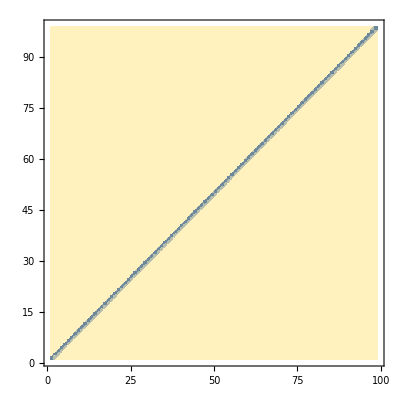

```mathematica
ListDensityPlot[JacobiSim2Table[Prime[Range[2,100]]]]
```

https://en.wikipedia.org/wiki/Quadratic_reciprocity
-Graphics-

-Graphics-
https://youtu.be/X63MWZIN3gM
Why did they prove this amazing theorem in 200 different ways? Quadratic Reciprocity MASTERCLASS

### Jacobi Symbol – extension of Legendre Symbol for not primes

JacobiSymbol[m, p] == If[("x^2==m mod p" has solutions), 1, -1]

```mathematica
a =3 3 3 ; b =5 5 ; c= 7;
JacobiSymbol[a * b, c] == JacobiSymbol[a, c]*JacobiSymbol[b, c]
JacobiSymbol[c,a * b] == JacobiSymbol[c, a]*JacobiSymbol[c, b]
```

True

True

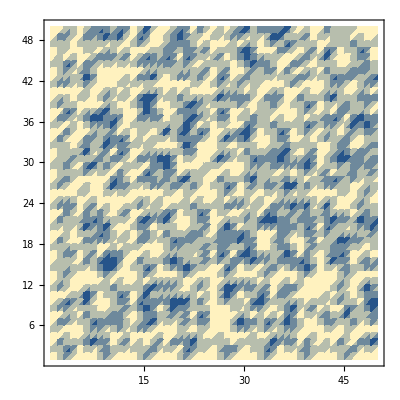

```mathematica
ListDensityPlot[JacobiTable[Range[1,100,2]]]
```

### Solutions for x^2+b x +c==0

```mathematica
(x-b/2)^2+c -b^2/4 == 0
```

-597/4+(-25/2+x)^2==0

has solutions == HasSqSolution[p, b^2/4-c];
p==2 is special case, because 1/2 == 1/ 0

### Circle, or solutions for x^2+y^2 =a

```mathematica
x^2+y^2==1
```

x^2+y^2==1

```mathematica
Solve[x^2+y^2==1,{x,y},Modulus->7]
```

{{x→0,y→1},{x→0,y→6},{x→1,y→0},{x→2,y→2},{x→2,y→5},{x→5,y→2},{x→5,y→5},{x→6,y→0}}

```mathematica
CircleSolutions[p_,a_]:=CircleSolutions[p,a]=Length[Solve[x^2+y^2==a,{x,y},Modulus->p]];
```

```mathematica
p=117;
l={x,y}/.Solve[x^2+y^2==10,{x,y},Modulus->p]
```

{{0,19},{0,46},{0,71},{0,98},{1,3},{1,36},{1,42},{1,75},{1,81},{1,114},{3,1},{3,53},{3,64},{3,116},{6,26},{6,91},{10,12},{10,27},{10,51},{10,66},{10,90},{10,105},{12,10},{12,55},{12,62},{12,107},{19,0},{19,39},{19,78},{26,6},{26,33},{26,45},{26,72},{26,84},{26,111},{27,10},{27,55},{27,62},{27,107},{33,26},{33,91},{36,1},{36,53},{36,64},{36,116},{39,19},{39,46},{39,71},{39,98},{42,1},{42,53},{42,64},{42,116},{45,26},{45,91},{46,0},{46,39},{46,78},{51,10},{51,55},{51,62},{51,107},{53,3},{53,36},{53,42},{53,75},{53,81},{53,114},{55,12},{55,27},{55,51},{55,66},{55,90},{55,105},{62,12},{62,27},{62,51},{62,66},{62,90},{62,105},{64,3},{64,36},{64,42},{64,75},{64,81},{64,114},{66,10},{66,55},{66,62},{66,107},{71,0},{71,39},{71,78},{72,26},{72,91},{75,1},{75,53},{75,64},{75,116},{78,19},{78,46},{78,71},{78,98},{81,1},{81,53},{81,64},{81,116},{84,26},{84,91},{90,10},{90,55},{90,62},{90,107},{91,6},{91,33},{91,45},{91,72},{91,84},{91,111},{98,0},{98,39},{98,78},{105,10},{105,55},{105,62},{105,107},{107,12},{107,27},{107,51},{107,66},{107,90},{107,105},{111,26},{111,91},{114,1},{114,53},{114,64},{114,116},{116,3},{116,36},{116,42},{116,75},{116,81},{116,114}}

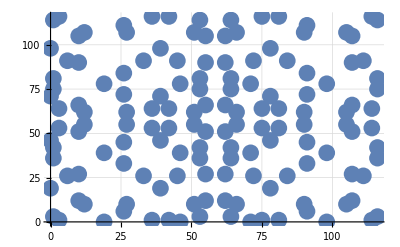

```mathematica
ListPlot[l,PlotStyle->{PointSize[0.03]}]
```

```mathematica
p=67;
l={x,y}/.Solve[x^2+y^2==1,{x,y},Modulus->p];
a = Table[0,{i,p},{j,p}];
({i,j}=#; a⟦i+1,j+1⟧=1;)&/@l;
ArrayPlot[a,Mesh->All]
```

-Graphics-

```mathematica
PrimitiveRootList[23]
```

{5,7,10,11,14,15,17,19,20,21}

```mathematica
Manipulate[Block[{p,l,arr,i1,j1,i2,j2,roots},
p=Prime[pi];
l={x,y}/.Solve[x^2+y^2==r,{x,y},Modulus->p];
arr = Table[0,{i,p},{j,p}];
(
{i1,j1}=#;
i2=Mod[ap i1 + bp,p];
j2=Mod[ap j1 + bp,p];
 arr⟦i2+1,j2+1⟧=1;)&/@l;
ArrayPlot[arr,PlotLabel->p]
],
{{pi,9},1,100,1},
{{ap,1},1,Prime[pi]-1,1},
{{bp,(Prime[pi]-1)/2},0,Prime[pi]-1,1},
{{r,1},0,Prime[pi]-1,1}
]
```

Disk

```mathematica
Manipulate[Block[{p,l,arr,i,j,i1,j1,i2,j2,roots},
p=Prime[pi];
roots=PrimitiveRootList[p];
ri=Mod[ri,Length[roots]+1];
l={x,y}/.Solve[x^2+y^2==1,{x,y},Modulus->p];
arr = Table[
{i1,j1}=If[ri==0,{i,j},{If[i==0,i,roots⟦ri⟧^i],If[j==0,0,roots⟦ri⟧^j]}];
i2=Mod[ap i1 + bp,p];
j2=Mod[ap j1 + bp,p];
-JacobiSymbol[i2^2+j2^2-1,p],{i,p},{j,p}
];
ArrayPlot[arr,PlotLabel->p]
],
{{pi,9},1,100,1},
{{ri,0},0,Prime[pi]-1,1},
{{ap,1},1,Prime[pi]-1,1},
{{bp,0},0,Prime[pi]-1,1}
]
```

```mathematica
circN={#,CircleSolutions[#,1]}&/@Prime[Range[100]];
```

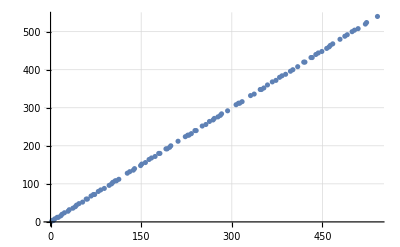

```mathematica
ListPlot[circN]
```

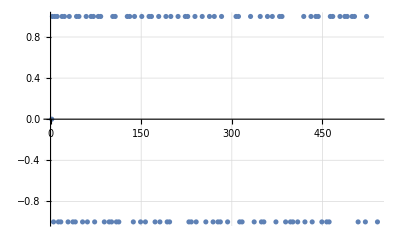

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-#⟦1⟧}&/@circN]
```

```mathematica
JacobiSymbol[-1,ps]
```

{1,-1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,-1,1,-1,-1,1,-1,-1,1,1,1,-1,9946,1,-1,-1,1,-1,1,-1,1,-1,1,-1,1,1,-1,-1,-1,-1,1,1,-1,1,1,-1,-1,1,-1,1}
 |  |  |  |

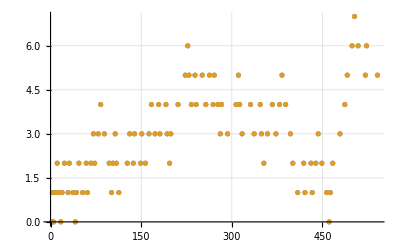

```mathematica
{ps,cs}=({#⟦1⟧,#⟦2⟧-#⟦1⟧}&/@circN)ᵀ;
ListPlot[{
{ps,Accumulate[cs]}ᵀ, {ps,1-Accumulate[JacobiSymbol[-1,ps]]}ᵀ
}]
```

```mathematica
(
p=#;
{CircleSolutions[p,1]-p,-JacobiSymbol[-1,p]}
)&/@Prime[Range[20]]
```

{{0,-1},{1,1},{-1,-1},{1,1},{1,1},{-1,-1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{1,1},{1,1}}

```mathematica
CircleSolutions[2,1]
```

2

```mathematica
CircleSolutions[p_,1]:=p-If[p==2,0,JacobiSymbol[-1,p]]
```

```mathematica
circN={#,CircleSolutions[#,2]}&/@Prime[Range[100]];
```

```mathematica
ListPlot[circN]
```

-Graphics-

```mathematica
ListPlot[{#⟦1⟧,#⟦2⟧-#⟦1⟧}&/@circN]
```

-Graphics-

```mathematica
(
p=#;
{CircleSolutions[p,3]-p,-JacobiSymbol[-1,p]}
)&/@Prime[Range[20]]
```

{{0,-1},{-2,1},{-1,-1},{1,1},{1,1},{-1,-1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{1,1},{1,1}}

```mathematica
(
p=#;
{CircleSolutions[p,5]-p,-JacobiSymbol[-1,p]}
)&/@Prime[Range[20]]
```

{{0,-1},{1,1},{4,-1},{1,1},{1,1},{-1,-1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{-1,-1},{1,1},{1,1},{-1,-1},{1,1},{-1,-1},{1,1},{1,1}}

```mathematica
CircleSolutions[2,2]
```

2

```mathematica
CircleSolutionsF[p_,a_]:=If[
p==2, p,
If[Mod[a,p]==0,1,p-JacobiSymbol[-1,p]]
];
```

```mathematica
CircleSolutionsF[p_,a_]:=If[
p==2, p,
If[Mod[a,p]==0,1,p-JacobiSymbol[-1,p]]
];
```

```mathematica
primes=Prime[Range[20]];

(Table[
CircleSolutionsF[primes⟦i⟧,a]==CircleSolutions[primes⟦i⟧,a],
{i,Length[primes]},
{a,0,i-1}
]//Flatten)
```

{True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
primes=Prime[Range[20]];

(Table[
{primes⟦i⟧, a,CircleSolutionsF[primes⟦i⟧,a],CircleSolutions[primes⟦i⟧,a],CircleSolutionsF[primes⟦i⟧,a]==CircleSolutions[primes⟦i⟧,a]},
{i,Length[primes]},
{a,0,i-1}
])//Flatten[#,1]&//Select[#,(!#[[-1]])&]&
```

{{5,0,1,9,False},{13,0,1,25,False},{17,0,1,33,False},{29,0,1,57,False},{37,0,1,73,False},{41,0,1,81,False},{53,0,1,105,False},{61,0,1,121,False}}

```mathematica
(Table[
{primes⟦i⟧, a,CircleSolutionsF[primes⟦i⟧,a],CircleSolutions[primes⟦i⟧,a],CircleSolutionsF[primes⟦i⟧,a]==CircleSolutions[primes⟦i⟧,a]},
{i,Length[primes]},
{a,0,0}
])//Flatten[#,1]&
```

{{2,0,2,2,True},{3,0,1,1,True},{5,0,1,9,False},{7,0,1,1,True},{11,0,1,1,True},{13,0,1,25,False},{17,0,1,33,False},{19,0,1,1,True},{23,0,1,1,True},{29,0,1,57,False},{31,0,1,1,True},{37,0,1,73,False},{41,0,1,81,False},{43,0,1,1,True},{47,0,1,1,True},{53,0,1,105,False},{59,0,1,1,True},{61,0,1,121,False},{67,0,1,1,True},{71,0,1,1,True}}

```mathematica
CircleSolutionsF[p_,a_]:=If[
p==2, p,
If[
Mod[a,p]==0,
If[JacobiSymbol[-1,p]==-1,1,2 p -1],
p-JacobiSymbol[-1,p]]
];
```

It takes long time :

```mathematica
(*

primes=Prime[Range[150]];
(Table[
{primes⟦i⟧, a,CircleSolutionsF[primes⟦i⟧,a],CircleSolutions[primes⟦i⟧,a],CircleSolutionsF[primes⟦i⟧,a]==CircleSolutions[primes⟦i⟧,a]},
{i,Length[primes]},
{a,1,i}
])//Flatten[#,1]&//Select[#,(!#⟦-1⟧)&]&//Timing

*)
```

$Aborted

### Other quadratics

```mathematica
Manipulate[
p=Prime[pi];
l={x,y}/.Solve[x^2-y==1,{x,y},Modulus->p];
aa = Table[0,{i,p},{j,p}];
({i,j}=#; aa⟦i+1,j+1⟧=1;)&/@l;
ArrayPlot[aa,PlotLabel->p],
{{pi,4},1,100,1}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

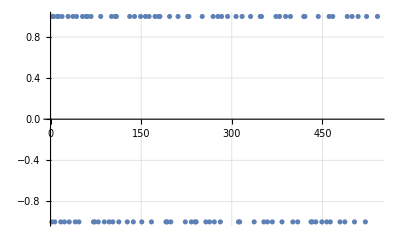

```mathematica
ll=(
p=#;
{p,Length[Solve[x^2-2 y^2==1,{x,y},Modulus->p]]-p}
)&/@Prime[Range[100]];
ListPlot[ll]
```

```mathematica
ll=(
p=#;
{p,Length[Solve[x^2-2 y^2==2,{x,y},Modulus->p]]-p}
)&/@Prime[Range[100]];
ListPlot[ll]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

-Graphics-

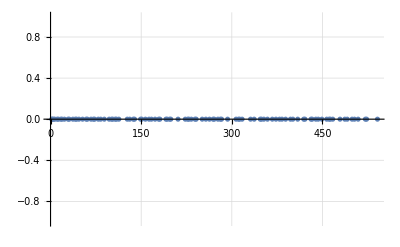

```mathematica
ll=(
p=#;
{p,Length[Solve[x^2-y==1,{x,y},Modulus->p]]-p}
)&/@Prime[Range[100]];
ListPlot[ll]
```

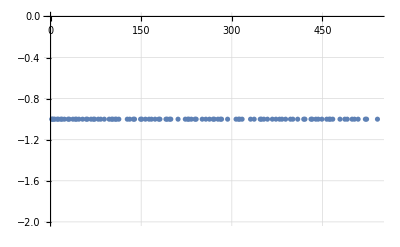

```mathematica
ll=(
p=#;
{p,Length[Solve[x y==1,{x,y},Modulus->p]]-p}
)&/@Prime[Range[100]];
ListPlot[ll]
```

### Solutions for x^3+b x +c=0

```mathematica
CubicSolutions[p_,b_,c_]:=CubicSolutions[p,b,c]=Length[Solve[x^3+b x +c==0,x,Modulus->p]];
```

```mathematica
{#,CubicSolutions[#,1,1]}&/@Prime[Range[30]]
```

{{2,0},{3,1},{5,0},{7,0},{11,1},{13,1},{17,1},{19,0},{23,1},{29,1},{31,3},{37,1},{41,0},{43,1},{47,3},{53,1},{59,0},{61,1},{67,3},{71,0},{73,1},{79,1},{83,1},{89,1},{97,0},{101,0},{103,0},{107,0},{109,0},{113,0}}

```mathematica
l={#,CubicSolutions[#,1,1]}&/@Prime[Range[90]]//Select[#,((#⟦2⟧==3)&)]&
```

{{31,3},{47,3},{67,3},{131,3},{149,3},{173,3},{227,3},{283,3},{293,3},{349,3},{379,3},{431,3}}

```mathematica
l={#,CubicSolutions[#,1,1]}&/@Prime[Range[90]]//Select[#,((#⟦2⟧==0)&)]&
```

{{2,0},{5,0},{7,0},{19,0},{41,0},{59,0},{71,0},{97,0},{101,0},{103,0},{107,0},{109,0},{113,0},{157,0},{163,0},{191,0},{193,0},{211,0},{233,0},{257,0},{281,0},{307,0},{311,0},{317,0},{359,0},{373,0},{397,0},{419,0},{421,0},{439,0},{443,0}}

```mathematica
l={#,CubicSolutions[#,1,1]}&/@Prime[Range[90]]//Select[#,((#⟦2⟧==1)&)]&
```

{{3,1},{11,1},{13,1},{17,1},{23,1},{29,1},{37,1},{43,1},{53,1},{61,1},{73,1},{79,1},{83,1},{89,1},{127,1},{137,1},{139,1},{151,1},{167,1},{179,1},{181,1},{197,1},{199,1},{223,1},{229,1},{239,1},{241,1},{251,1},{263,1},{269,1},{271,1},{277,1},{313,1},{331,1},{337,1},{347,1},{353,1},{367,1},{383,1},{389,1},{401,1},{409,1},{433,1},{449,1},{457,1},{461,1},{463,1}}

```mathematica
Tally[CubicSolutions[#,1,1]&/@Prime[Range[90]]]
```

{{0,31},{1,47},{3,12}}

```mathematica
Tally[CubicSolutions[#,-1,1]&/@Prime[Range[90]]]
```

{{0,31},{1,46},{3,13}}

```mathematica
Tally[CubicSolutions[#,1,-1]&/@Prime[Range[90]]]
```

{{0,31},{1,47},{3,12}}

```mathematica
Tally[CubicSolutions[#,-1,-1]&/@Prime[Range[90]]]
```

{{0,31},{1,46},{3,13}}

```mathematica
Solve[x^3-x -1==0,x,Cubics->True]//N
```

{{x→1.32472},{x→-0.662359+0.56228 ⅈ},{x→-0.662359-0.56228 ⅈ}}

```mathematica
Solve[x^3-x -1==0,x,Cubics->True]
```

{{x→1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3)},{x→-1/6 (1+ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1-ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))},{x→-1/6 (1-ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1+ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))}}

```mathematica
data={{Mod[(#-1)/2,4],JacobiSymbol[69,#],JacobiSymbol[-1,#],JacobiSymbol[3,#],JacobiSymbol[-3,#]},CubicSolutions[#,-1,-1]}&/@Prime[Range[10000]];
```

```mathematica
{fs,target}=dataᵀ;
```

```mathematica
StandardDeviation[target]//N
```

0.994614

```mathematica
model=Predict[fs-> target];
Information[model]
```

PredictorFunction::mlbddataev: The data being evaluated is not formatted correctly.

Information[PredictorFunction[…][LossFunction,AcceptanceThreshold→Automatic,AnomalyDetector→None,BatchProcessing→Automatic,IndeterminateThreshold→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234,TargetDevice→CPU,UtilityFunction→Automatic,ValuePriors→Automatic]]

```mathematica
Tally[CubicSolutions[#,-3,1]&/@Prime[Range[90]]]//Sort
```

{{0,63},{3,27}}

```mathematica
Tally[CubicSolutions[#,-3,1]&/@Prime[Range[3000]]]//Sort
```

{{0,1995},{3,1005}}

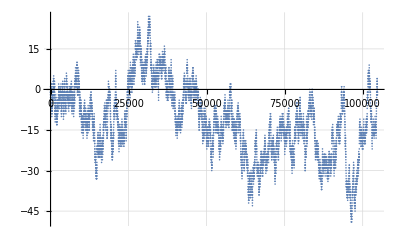

```mathematica
primes=Prime[Range[10000]];
t=(CubicSolutions[#,-3,1]-1)&/@primes;
ListPlot[{primes,Accumulate[t]}ᵀ]
```

```mathematica
Solve[x^3-3x +1==0,x,Cubics->True]
```

{{x→1/(1/2 (-1+ⅈ √3))^(1/3)+(1/2 (-1+ⅈ √3))^(1/3)},{x→-(1-ⅈ √3)/(2^(2/3) (-1+ⅈ √3)^(1/3))-1/2 (1/2 (-1+ⅈ √3))^(1/3) (1+ⅈ √3)},{x→-1/2 (1-ⅈ √3) (1/2 (-1+ⅈ √3))^(1/3)-(1+ⅈ √3)/(2^(2/3) (-1+ⅈ √3)^(1/3))}}

```mathematica
{JacobiSymbol[-3,#],JacobiSymbol[-4,#],JacobiSymbol[3,#],JacobiSymbol[2,#],JacobiSymbol[-1,#],CubicSolutions[#,-3,1]}&/@Prime[Range[90]]//Select[#,(#[[-1]]==3)&]&//Grid
```

0 | -1 | 0 | -1 | -1 | 3
-1 | 1 | -1 | 1 | 1 | 3
1 | -1 | -1 | -1 | -1 | 3
1 | 1 | 1 | -1 | 1 | 3
-1 | 1 | -1 | -1 | 1 | 3
-1 | -1 | 1 | 1 | -1 | 3
1 | 1 | 1 | 1 | 1 | 3
-1 | 1 | -1 | 1 | 1 | 3
-1 | -1 | 1 | -1 | -1 | 3
1 | 1 | 1 | -1 | 1 | 3
1 | -1 | -1 | 1 | -1 | 3
1 | -1 | -1 | -1 | -1 | 3
-1 | -1 | 1 | -1 | -1 | 3
1 | 1 | 1 | -1 | 1 | 3
-1 | 1 | -1 | -1 | 1 | 3
1 | -1 | -1 | 1 | -1 | 3
-1 | 1 | -1 | 1 | 1 | 3
-1 | -1 | 1 | -1 | -1 | 3
-1 | 1 | -1 | -1 | 1 | 3
1 | -1 | -1 | 1 | -1 | 3
1 | -1 | -1 | -1 | -1 | 3
-1 | -1 | 1 | 1 | -1 | 3
1 | -1 | -1 | -1 | -1 | 3
1 | 1 | 1 | -1 | 1 | 3
-1 | -1 | 1 | 1 | -1 | 3
1 | 1 | 1 | 1 | 1 | 3
-1 | 1 | -1 | 1 | 1 | 3

```mathematica
data={{Mod[(p-1)/2,3],Mod[(p-1)/2,5],JacobiSymbol[-3,#],JacobiSymbol[-4,#],JacobiSymbol[3,#],JacobiSymbol[2,#],JacobiSymbol[-1,#]},CubicSolutions[#,-3,1]}&/@Prime[Range[3000]];
{fs,target}=dataᵀ;
```

```mathematica
StandardDeviation[N[target]]
```

1.41621

```mathematica
model=Predict[fs->target];
Information[model]
```

Predictor information
Data type | Mixed (number: 7)
Standard deviation | 1.43 ± 0.029
Method | LinearRegression
Single evaluation time | 1.85 ms/example
Batch evaluation speed | 174. examples/ms
Loss | 1.79 ± 0.021
Model memory | 313. kB
Training examples used | 3000 examples
Training time | 1.5 s
 |

```mathematica
fakeModel=Predict[fs->RandomSample[target]];
Information[fakeModel]
```

Predictor information
Data type | Mixed (number: 7)
Standard deviation | 1.42 ± 0.024
Method | LinearRegression
Single evaluation time | 1.81 ms/example
Batch evaluation speed | 176. examples/ms
Loss | 1.78 ± 0.017
Model memory | 315. kB
Training examples used | 3000 examples
Training time | 1.48 s
 |

```mathematica
Solve[x^3-3x +1==0,x,Cubics->True]//N
```

{{x→1.53209+0. ⅈ},{x→0.347296+0. ⅈ},{x→-1.87939+0. ⅈ}}

```mathematica
Tally[CubicSolutions[#,3,1]&/@Prime[Range[90]]]//Sort
```

{{0,30},{1,47},{3,13}}

```mathematica
Tally[CubicSolutions[#,2,3]&/@Prime[Range[90]]]//Sort
```

{{1,46},{3,44}}

```mathematica
Tally[CubicSolutions[#,2,-3]&/@Prime[Range[90]]]//Sort
```

{{1,46},{3,44}}

```mathematica
Solve[x^3+2x+3==0,x]
```

{{x→-1},{x→1/2 (1-ⅈ √11)},{x→1/2 (1+ⅈ √11)}}

```mathematica
Solve[x^3+2x-3==0,x]
```

{{x→1},{x→1/2 (-1-ⅈ √11)},{x→1/2 (-1+ⅈ √11)}}

```mathematica
Solve[x^3-4x-15==0,x]
```

{{x→3},{x→1/2 (-3-ⅈ √11)},{x→1/2 (-3+ⅈ √11)}}

```mathematica
Tally[CubicSolutions[#,-4,-15]&/@Prime[Range[90]]]//Sort
```

{{1,46},{3,44}}

```mathematica
Tally[CubicSolutions[#,-4,-1]&/@Prime[Range[90]]]//Sort
```

{{0,32},{1,45},{3,13}}

```mathematica
Tally[CubicSolutions[#,0,1]&/@Prime[Range[90]]]//Sort
```

{{1,46},{3,44}}

```mathematica
Tally[CubicSolutions[#,0,-1]&/@Prime[Range[90]]]//Sort
```

{{1,46},{3,44}}

```mathematica
Tally[CubicSolutions[#,0,2]&/@Prime[Range[90]]]//Sort
```

{{0,29},{1,45},{3,16}}

```mathematica
Tally[CubicSolutions[#,0,3]&/@Prime[Range[90]]]//Sort
```

{{0,33},{1,46},{3,11}}

### More tables

```mathematica
n=50;
primes=Prime[Range[n]];
m=Max[primes];
arr=Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
1+JacobiSymbol[p,q]JacobiSymbol[q,p],
{j,1,n},
{i,1,n}
];
ArrayPlot[arr]
```

-Graphics-

```mathematica
arr=Table[
1+JacobiSymbol[q,p]JacobiSymbol[p,q](-1)^((p-1)/2(q-1)/2),
{p,3,100,2},
{q,3,100,2}
];
ArrayPlot[arr]
```

-Graphics-

```mathematica
arr=Table[
1+JacobiSymbol[1-p,q]JacobiSymbol[p,q],
{p,2,100},
{q,2,100}
];
ArrayPlot[arr]
```

-Graphics-

```mathematica
n=150;
primes=Prime[Range[n]];
m=Max[primes];
arr=Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
1+JacobiSymbol[p-1,q]JacobiSymbol[q-1,p],
{j,1,n},
{i,1,n}
];
ArrayPlot[arr]
```

-Graphics-

```mathematica
n=150;
primes=Prime[Range[n]];
m=Max[primes];
arr=Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
1+JacobiSymbol[p-1,q]JacobiSymbol[q-1,p],
{j,1,n},
{i,1,n}
];
ArrayPlot[arr]
```

-Graphics-

```mathematica
n=50;
primes=Prime[Range[n]];
m=Max[primes];
arr=Table[
p=primes⟦i⟧;
q=primes⟦j⟧;
1+JacobiSymbol[p-1,q]JacobiSymbol[p,q],
{j,1,n},
{i,1,n}
];
ArrayPlot[arr]
```

-Graphics-